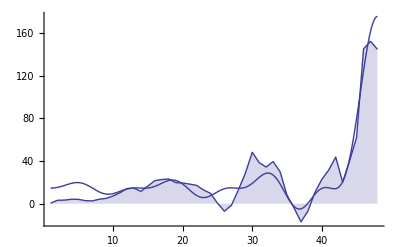

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

Indeterminate

```mathematica
debtgrowth={0.4400,3.1982,3.3743,4.1771,4.1190,2.8467,2.6322,4.1904,5.0231,7.2800,10.3453,14.2288,14.5533,11.5171,16.6372,21.6328,22.7073,23.1794,19.8064,19.3560,18.4091,17.1979,12.8715,9.6976,0.5134,-7.0923,-1.5162,12.8463,28.4999,48.2350,38.5317,34.4336,39.5281,30.0362,7.8871,-3.8499,-17.0916,-7.0828,10.5399,22.7527,31.7045,43.7520,20.1719,40.4446,62.2287,145.4002,152.4235,144.8785};
g1=ListLinePlot[debtgrowth, Filling->Axis, PlotRange->All];
m=0.46;
n=48;
shift=14.67;
cossh = 0.579;
cosmul = 0.654;
mul = 130.66;
proto[x_]= shift+(cossh+cosmul*Cos[m x- m n])mul Sin[m x-m n]/(m x-m n) ;
g2=Plot[proto[x],{x,1,48}, PlotRange->All];
Show[g1,g2]
Correlation[debtgrowth, Table[proto[x],{x,1,48}]]
```

```mathematica
Table[10+140Sin[(m x-d2)/d]/((m x-d2)/d),{x,1,48}]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

{14.3853,16.2235,16.8635,16.1203,14.0826,11.1069,7.75793,4.70387,2.58603,1.88759,2.82765,5.30301,8.89181,12.9212,16.5893,19.1195,19.9191,18.7097,15.6043,11.1092,6.04978,1.42644,-1.77286,-2.7715,-1.17577,2.91567,8.88994,15.6961,22.0125,26.4795,27.9616,25.7894,19.9392,11.1106,0.683261,-9.45139,-17.1595,-20.3986,-17.5621,-7.77815,8.88901,31.3727,57.6898,85.1722,110.811,131.666,145.273,Indeterminate}

```mathematica
{0.4400,3.1982,3.3743,4.1771,4.1190,2.8467,2.6322,4.1904,5.0231,7.2800,10.3453,14.2288,14.5533,11.5171,16.6372,21.6328,22.7073,23.1794,19.8064,19.3560,18.4091,17.1979,12.8715,9.6976,0.5134,-7.0923,-1.5162,12.8463,28.4999,48.2350,38.5317,34.4336,39.5281,30.0362,7.8871,-3.8499,-17.0916,-7.0828,10.5399,22.7527,31.7045,43.7520,20.1719,40.4446,62.2287,145.4002,152.4235,144.8785}/{14.385304763712618,16.223516132037627,16.863495124508297,16.1203176873576,14.082594323078023,11.106904865160214,7.757930541444873,4.703865348509642,2.586029290167022,1.887594187677328,2.827648324594686,5.303012900296422,8.891810908030532,12.921228216356333,16.58932248904042,19.119541975117816,19.919059686997564,18.709747597585178,15.604300463731635,11.109240487204893,6.049780105205256,1.4264402451678144,-1.7728602232990927,-2.771502579748569,-1.1757741724891257,2.9156710356984146,8.889941347491416,15.696137439344632,22.01245625085766,26.47954267721935,27.961627730389445,25.78942689133712,19.93915463151468,11.110643277860065,0.6832612027353271,-9.451385394589455,-17.159515619527575,-20.398641678536983,-17.562143056489706,-7.778154373047261,8.889005858283731,31.37265991118507,57.689829952151335,85.17221889640282,110.81105260593823,131.66553259633798,145.2733179892488,150}
```

{0.0305868,0.197134,0.200095,0.25912,0.292489,0.2563,0.339292,0.890842,1.9424,3.85676,3.65862,2.68315,1.63671,0.891332,1.00289,1.13145,1.13998,1.23889,1.26929,1.74233,3.04294,12.0565,-7.2603,-3.49904,-0.436648,-2.43248,-0.170552,0.818437,1.29472,1.82159,1.37802,1.33518,1.98244,2.70337,11.5433,0.407337,0.996042,0.347219,-0.600149,-2.92521,3.56671,1.39459,0.349661,0.474857,0.561575,1.10431,1.04922,0.965857}

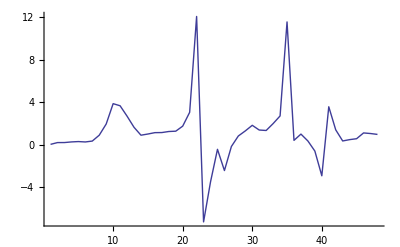

```mathematica
ListLinePlot[{0.030586769430837074,0.19713359138493458,0.2000949373238774,0.2591202035227818,0.29248872086373595,0.256300025484997,0.3392915141400282,0.8908418267813881,1.942398726533982,3.856761187084387,3.658623284238464,2.6831539480518054,1.6367082195659786,0.8913316758403108,1.0028860437785334,1.1314496983323628,1.139978510874311,1.2388943185418337,1.2692911192036527,1.7423333325345998,3.042937045622655,12.056516253140868,-7.260301647496829,-3.499040582123422,-0.43664847554282216,-2.432476062341897,-0.17055230633527688,0.8184370230983641,1.2947169400456877,1.8215949039594674,1.378020634976222,1.3351828307424127,1.9824361027585473,2.7033718254506898,11.543316038471458,0.4073371087167725,0.9960421015934572,0.34721919780827226,-0.6001488523409567,-2.9252055061856703,3.5667093154691014,1.3945900705856764,0.3496612837432668,0.47485671412639624,0.5615748477843198,1.1043148281317479,1.0492188249688106,0.9658566666666667},PlotRange->All]
```

```mathematica
Correlation[{0.21,0.9,0.65,2.2,-0.21,-0.9,0.36,2.4,1.04,3.58,5.94,10.19,10.58,12.01,7.7,11.32,15.6,11.4,7.3,11.3,13.4,5.5,5.1,-0.4,-13.5,-1.7,-0.9,14.8,36.5,47.2,40.2,32.1,25.9,4.9,-1.3,-6.2,-33,3.1,31.6,35.7,41.2,39,37,25,91.9,142.6,145.8,133.7}, {0.4400,3.1982,3.3743,4.1771,4.1190,2.8467,2.6322,4.1904,5.0231,7.2800,10.3453,14.2288,14.5533,11.5171,16.6372,21.6328,22.7073,23.1794,19.8064,19.3560,18.4091,17.1979,12.8715,9.6976,0.5134,-7.0923,-1.5162,12.8463,28.4999,48.2350,38.5317,34.4336,39.5281,30.0362,7.8871,-3.8499,-17.0916,-7.0828,10.5399,22.7527,31.7045,43.7520,20.1719,40.4446,62.2287,145.4002,152.4235,144.8785}]
```

0.964034

```mathematica
Correlation[{12.7400,14.1200,15.2900,17.4900,19.0900,19.7900,21.6000,24.2400,26.3900,30.5500,39.2200,51.5200,58.4600,61.8700,71.9500,85.1700,103.8600,116.0600,128.0400,132.7000,140.5000,150.9000,158.6000,164.6000,173.6000,179.9000,200.9000,218.2000,236.2000,259.7300,266.6700,284.0300,304.3300,312.3900,318.4300,328.1100,338.0700,362.5700,384.9300,415.2100,451.5000,488.3100,502.5600,543.9600,575.9700,621.4000,660.8100,681.3300}, {12.30,10.92,11.92,13.31,14.97,16.94,18.97,20.05,21.37,23.27,28.87,37.29,43.91,50.35,55.31,63.54,81.15,92.88,108.23,113.34,122.09,133.70,145.73,154.90,173.09,186.99,202.42,205.35,207.70,211.50,228.14,249.60,264.80,282.35,310.54,331.96,355.16,369.65,374.39,392.46,419.80,444.56,482.39,503.52,513.74,476.00,508.39,536.45}]
```

0.988714

```mathematica
NonlinearModelFit
```

```mathematica
FindFit[{0.4400,3.1982,3.3743,4.1771,4.1190,2.8467,2.6322,4.1904,5.0231,7.2800,10.3453,14.2288,14.5533,11.5171,16.6372,21.6328,22.7073,23.1794,19.8064,19.3560,18.4091,17.1979,12.8715,9.6976,0.5134,-7.0923,-1.5162,12.8463,28.4999,48.2350,38.5317,34.4336,39.5281,30.0362,7.8871,-3.8499,-17.0916,-7.0828,10.5399,22.7527,31.7045,43.7520,20.1719,40.4446,62.2287,145.4002,152.4235,144.8785},a Sin[m x] + b Cos[n x]+c x^p,{a,b,c,n,m,p},x]
```

FindFit::ivar: 1.44 is not a valid variable.

```mathematica
FindFit[debtgrowth,c x^p+b Cos[n x]+a Sin[m x],{a,b,c,n,m,p},x,MaxIterations->100000]
```

{a→6.26962,b→3.8349,c→4.27256×10^-18,n→0.945112,m→0.65666,p→11.6559}

{6.07336,4.8587,2.12024,0.00917152,-0.834973,-1.35268,-2.60292,-4.2667,-4.61316,-2.08036,2.9001,7.56726,8.55051,4.4561,-2.73706,-8.72905,-9.77128,-5.26651,1.84748,7.20236,7.98541,4.59666,-0.115634,-3.22672,-3.7433,-2.7552,-1.88248,-1.57237,-0.803649,1.5928,5.29572,8.18267,7.85629,3.85554,-1.35327,-3.65343,-0.0490038,9.14367,20.435,29.6374,34.8875,38.0055,43.2788,54.7226,73.9557,100.201,132.156,170.047}

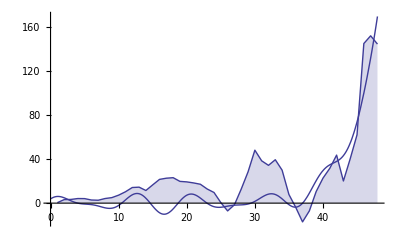

```mathematica
g2 = Plot[4.27256*(10^-18) x^11.6559+3.8349 Cos[0.945112 x]+6.26962 Sin[0.65666 x], {x, 0, 48}, PlotRange->All];
data = Table[4.27256*(10^-18) x^11.6559+3.8349 Cos[0.945112 x]+6.26962 Sin[0.65666 x], {x, 1, 48}]
Show[g1,g2]
```

0.925448

989.25

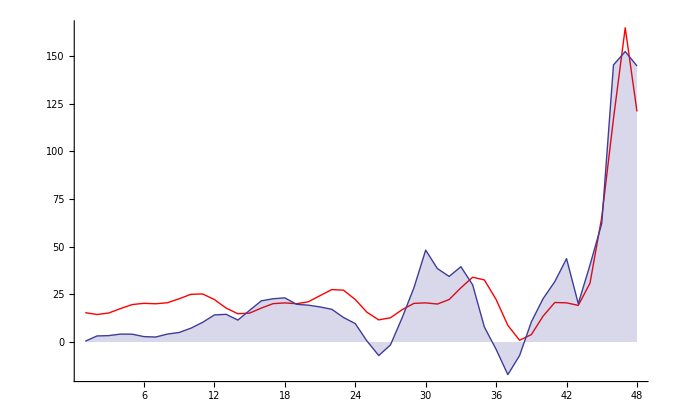

```mathematica
data={15.42,14.46,15.24,17.56,19.67,20.32,20.08,20.62,22.72,25.04,25.23,22.29,17.81,14.85,15.19,17.83,20.14,20.54,20.10,21.13,24.35,27.51,27.21,22.32,15.61,11.63,12.74,17.00,20.29,20.56,19.94,22.31,28.47,34.00,32.59,22.33,8.73,0.95,3.89,13.58,20.76,20.56,19.24,30.92,65.46,117.22,164.89,121.00
};
Correlation[data,debtgrowth]
Covariance[data,debtgrowth]
Show[ListLinePlot[data, PlotRange->All, PlotStyle->RGBColor[1,0,0]], ListLinePlot[debtgrowth, PlotRange->All,  Filling->Axis]
 ]
```

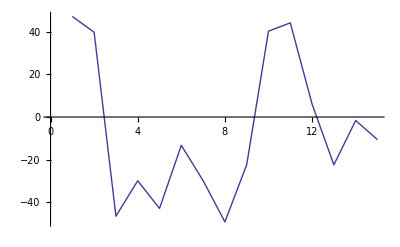

```mathematica
ListLinePlot[{47.060,39.660,-46.410,-29.830,-42.780,-13.270,-29.740,-49.080,-22.340,40.170,44.070,6.070,-22.360,-1.640,-10.560}]
```

```mathematica
Correlation[{-1.90,1.46,5.13,8.27,10.14,10.25,8.49,5.16,0.97,-3.17,-6.30,-7.65,-6.80,-3.82,0.73,5.90,10.51,13.48,14.01,11.79,7.15,0.97,-5.42,-10.57,-13.17,-12.38,-8.09,-0.93,7.71,15.98,21.91,23.83,20.79,12.79,0.97,-12.53,-24.87,-32.97,-34.04,-26.19,-8.77,17.33,49.75,84.93,118.61,146.49,164.88,171.30
},debtgrowth]
```

0.912873

```mathematica
Mean[debtgrowth]
```

23.9082

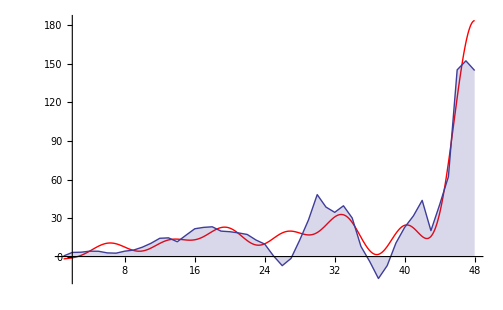

```mathematica
Show[Plot[-25.2/(1.04^(2 x))+21.24+(0.469+0.845*Cos[-0.47 x - (-0.47)48])*124.09*Sin[-0.47 x - (-0.47)48]/(-0.47 x - (-0.47)48),{x, 1, 48}, PlotRange->All,PlotStyle->RGBColor[1,0,0]], ListLinePlot[debtgrowth, Filling->Axis,PlotRange->All ]]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

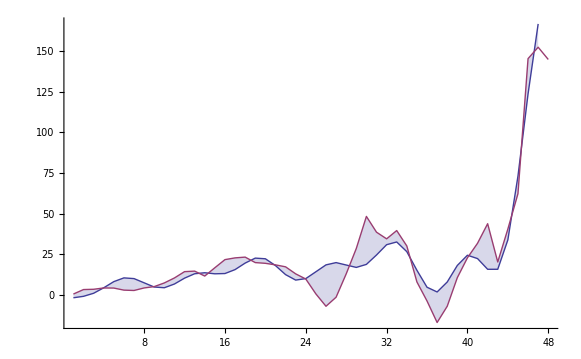

```mathematica
ListLinePlot[{Table[-25.2/(1.04^(2 x))+21.24+(0.469+0.845*Cos[-0.47 x - (-0.47)48])*124.09*Sin[-0.47 x - (-0.47)48]/(-0.47 x - (-0.47)48),{x, 1, 48} ], debtgrowth}, Filling->{1->{2}},PlotRange->All ]
```

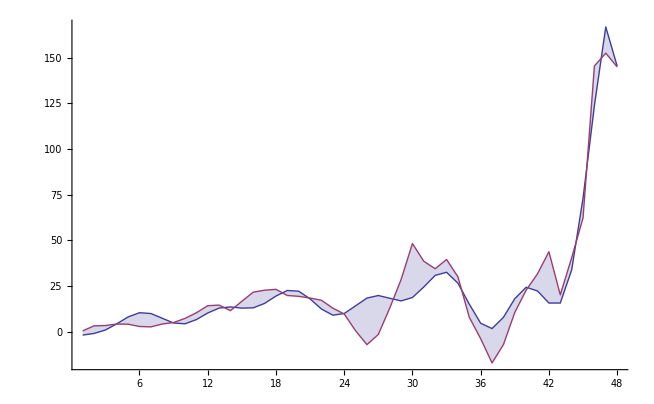

```mathematica
ListLinePlot[{{-1.85,-0.96,0.91,4.29,8.09,10.39,9.95,7.36,4.76,4.32,6.62,10.23,12.93,13.56,12.90,13.06,15.48,19.50,22.56,22.16,17.96,12.40,9.03,9.95,14.16,18.40,19.80,18.31,16.84,18.70,24.48,30.82,32.51,26.53,15.07,4.63,1.72,7.86,18.06,24.35,22.27,15.68,15.69,33.76,73.00,123.68,166.77,145.33}, debtgrowth}, Filling->{1->{2}},PlotRange->All ]
```

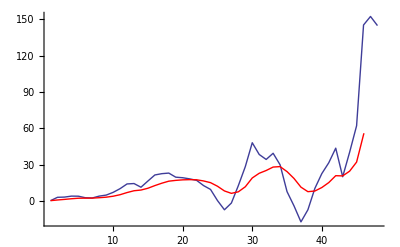

```mathematica
Show[ListLinePlot[debtgrowth,PlotRange->All],ListLinePlot[ExponentialMovingAverage[debtgrowth,0.2], PlotStyle->RGBColor[1,0,0]],PlotRange->All]
```

```mathematica
10000*8000*10000*10000*3000*200*200
```

960000000000000000000000

```mathematica
N[%]
```

9.6×10^23

```mathematica
Clear[m,m];Clear[n,n];Clear[d,d]
```

```mathematica
r=(a Sin[m t-m n] (b Cos[m t-m n]+c))/(m t-m n)-w/k^(v t)+u;

Simplify[%]
```

u-n^(-t v) w+(a (c+b Cos[m (n-t)]) Sin[m (n-t)])/(m (n-t))

```mathematica
Subscript[Y, t]=(a Sin[Subscript[d, t]] (b Cos[Subscript[d, t]]+c))/Subscript[d, t]-w/n^(v t)+u;
```

```mathematica
Subscript[d, t]=m t - m n;
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

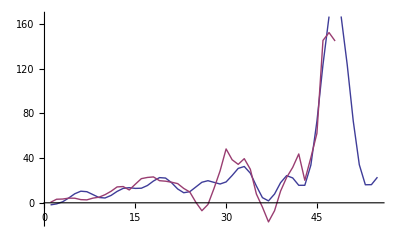

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

{-1.85265,-0.964005,0.911735,4.28836,8.09145,10.3895,9.94792,7.35623,4.7588,4.32141,6.61554,10.2257,12.9349,13.5561,12.9047,13.0631,15.4843,19.5004,22.5614,22.1593,17.9638,12.3964,9.02922,9.94892,14.1618,18.4003,19.7987,18.3147,16.8367,18.6961,24.4787,30.8221,32.506,26.5334,15.0673,4.6328,1.71935,7.85573,18.0562,24.3465,22.2743,15.6784,15.6877,33.7623,72.997,123.685,166.77,Indeterminate,166.862,123.869,73.2743,34.1346,16.1574,16.2483,22.9481}

```mathematica
Clear[u,u];Clear[a,a];Clear[m,m];Clear[c,c];Clear[b,b];Clear[w,w];Clear[k,k];Clear[v,v];Clear[n,n];
u=21.24;a=124.09;m=-0.47;c=0.469;b=0.845;w=25.2;k=1.04;v=2.00;
n=48;
ListLinePlot[{Table[(a Sin[m t-m n] (b Cos[m t-m n]+c))/(m t-m n)-w/k^(v t)+u,{t,1,n+7}], debtgrowth},PlotRange->All]
Table[(a Sin[m t-m n] (b Cos[m t-m n]+c))/(m t-m n)-w/k^(v t)+u,{t,1,n+7}]
Clear[u,u];Clear[a,a];Clear[m,m];Clear[c,c];Clear[b,b];Clear[w,w];Clear[k,k];Clear[v,v];Clear[n,n];
u=21.24;a=124.09;m=-0.47;c=0.469;b=0.845;w=25.2;k=1.04;v=2.00;
```

```mathematica
LeastSquares
```